# Simple Task 8

Brian Carlson 2-26-14

## Problem 1

Give the two functions g2[x] and f2[x] below. Show a graph of both functions containing all intersection points of the two functions.

```mathematica
f2[x_] := √(9.384*^-8 x^3+ -0.047 x^2+ 46.75 x + -11621.62)
```

```mathematica
g2[x_] := 3 Sin[ x/3] + 5
```

### A. Why the Original Explanation is Incorrect

#### The bad explanation:

Explanation: The function f2 cannot be negative, since it is a square root function. As can be seen from the above, the only x-range where f2[x] is positive is between 480 and 520. I also used NSolve to find where f2[x] is 0 and it returned the two values x = 516.143 and 480.025.Thus all the intersection points have to be within that range.  There are exactly four intersection points between f2[x] and g2[x].

#### Reasons why that explanation is bad:

1.) The above explanation makes the assumption that the function “f2” doesn’t exist in the imaginary plane when it’s possible that it could.
2.) The above explanation makes the assumption that the graph of “f2” has to intersect the x-axis on the edges of its existence.  
3.) The above explanation incorrectly states that there are only two places where “f2” equals zero, when there are in fact three places.
4.) The above explanation incorrectly states that there are only four intersection points between “f2” and “g2”, when there are five real roots and one imaginary root.

### B. Correct Graphs and Intersection Points

```mathematica
FindRoot[f2[x]-g2[x] ==0, {x,499857}]
```

{x→499856.}

```mathematica
Solve[D[f2[x],x]==0,x,WorkingPrecision->100]
```

{{x→498.083},{x→333404.}}

After finding the derivative, we can see that the graph exists in more places than the one previously stated.

```mathematica
Factor[-11621.62+46.75 x-0.047 x^2+9.384*^-8 x^3]
```

9.384×10^-8 (-499856.+1. x) (-516.143+1. x) (-480.025+1. x)

```mathematica
√((-499856.34742595564+1. x) (-516.1426676728523+1. x) (-480.0248253826197+1. x))
```

√((-499856.+1. x) (-516.143+1. x) (-480.025+1. x))

```mathematica
Simplify[√((-499856.34742595564+1. x) (-516.1426676728523+1. x) (-480.0248253826197+1. x))]
```

There are many ways to find where “f2” equals zero to know that the graph exists in multiple places.

```mathematica
Solve[f2[x] ==0,x,WorkingPrecision->100]
```

{{x→480.025},{x→516.143},{x→499856.}}

```mathematica
p[x_]:= f2[x]-g2[x]
```

```mathematica
p[499856.35007288222687]
```

-8.81218×10^-8

Here, we can see where the combined function is essentially zero, indicating an intersection.

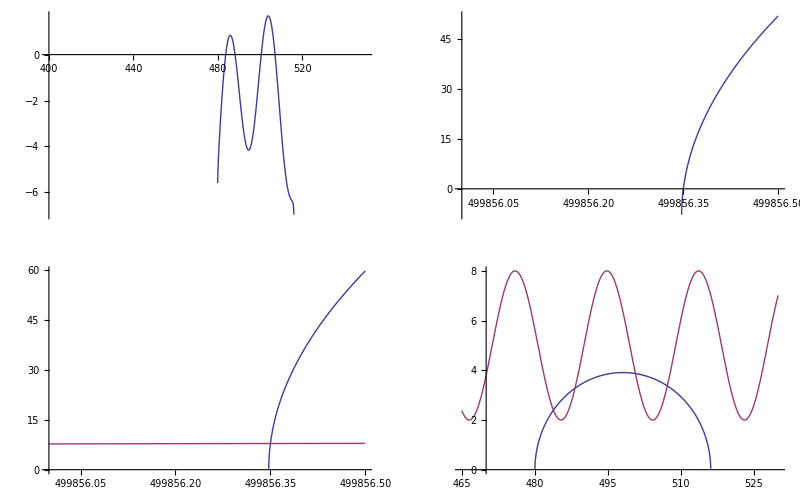

```mathematica
GraphicsGrid[{{Plot[f2[x]-g2[x],{x, 400, 550}],Plot[f2[x]-g2[x],{x,499856,499856.5},PlotPoints->150]},{Plot[{f2[x],g2[x]},{x,499856,499856.5}],Plot[{f2[x],g2[x]},{x, 465, 530}, PlotRange->{0,8}]}}]
```

Here, we can see that the graph has 5 real intersection points.

```mathematica
FindRoot[p[x] ==0, {x,485}]
```

{x→483.816}

```mathematica
FindRoot[p[x] ==0, {x,490}]
```

{x→488.256}

```mathematica
FindRoot[p[x] ==0, {x,500}]
```

{x→500.673}

```mathematica
FindRoot[p[x] ==0, {x,512}]
```

{x→507.218}

```mathematica
FindRoot[p[x] ==0, {x,499857}]
```

{x→499856.}

There’s also an intersection in the imaginary plane for these two functions.

```mathematica
FindRoot[p[x] ==0, {x,I}]
```

{x→-0.0617087+12.8261 ⅈ}

### C. A Better Explanation

After finding the roots of “f2[x]” and finding where its derivative equals zero, we can know that the graph exists nowhere else but around 498, 333404, 480.025, 516.143, and 499856.

Since we know that “g2[x]” is a periodic function that never crosses the x-axis, we know that we don’t have to worry about any intersections outside of the range of 2-8 for the entire graph.

We can be certain that these are the only intersection points because these are the only places where “f[x]-g2[x]” equals zero.

## Problem 2

Given two functions testMe[ ] and square[x]. Each of them uses a correct algorithm. However, calling the function testMe[ ] below causes a wrong result (see below). Find and correct the error.

```mathematica
square[x_ ] := 
Module[{sum=0},
For[i=1,i<2x, i= i+2, 
sum= sum+ i
];
Return[sum]
]
```

```mathematica
testMe[start_, stop_] := Module[{reslst={}},
For[ i=start, i≤ stop, i++,
      reslst =  Append[reslst, {i, square[i]}];
];
Return[reslst]
]
```

### A. The Problem with these Functions

The problem in question is simply an undeclared variable in “testMe” and/or “square”. If an “i” is added to the local variable declaration list in either functions, then the problem is resolved. However, it would be better coding to declare “i” in “square” as well as in “testMe” to prevent any problems in other pieces of code that may end up using the “square” or “testMe” functions.

Since we weren’t allowed to change the code in the algorithm, the only change that could be made was to the “testMe” function.

### B. Fixed Code

```mathematica
square[x_ ] := 
Module[{sum=0},
For[i=1,i< 2x, i= i+2, 
sum= sum+ i
];
Return[sum]
]
```

```mathematica
testMe[start_, stop_] := Module[{reslst={},i},
For[ i=start, i≤ stop, i++,
      reslst =  Append[reslst, {i, square[i]}];
];
Return[reslst]
]
```

#### Test Cases

```mathematica
testMe[7,22]
```

{{7,49},{8,64},{9,81},{10,100},{11,121},{12,144},{13,169},{14,196},{15,225},{16,256},{17,289},{18,324},{19,361},{20,400},{21,441},{22,484}}

```mathematica
testMe[23,34]
```

{{23,529},{24,576},{25,625},{26,676},{27,729},{28,784},{29,841},{30,900},{31,961},{32,1024},{33,1089},{34,1156}}

```mathematica
testMe[-1,17]
```

{{-1,0},{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100},{11,121},{12,144},{13,169},{14,196},{15,225},{16,256},{17,289}}